# Exact scattering diagram for KP2

```mathematica
SetDirectory[NotebookDirectory[]];
<<P2Scattering`
<<CoulombHiggs`
<<MaTeX`
```

P2Scattering 1.3 - A package for evaluating DT invariants on K_{P^2}

CoulombHiggs 6.3 - A package for evaluating quiver invariants

## Fundamental domain of Gamma_1(3) and its images

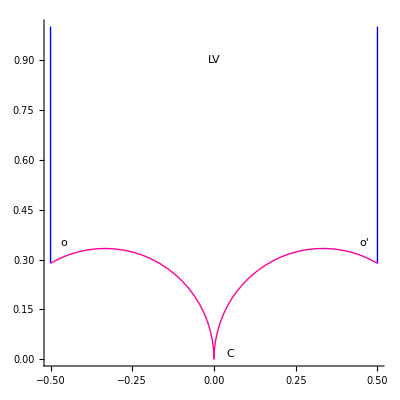

```mathematica
Show[FundDomainC[0],Axes->True]
```

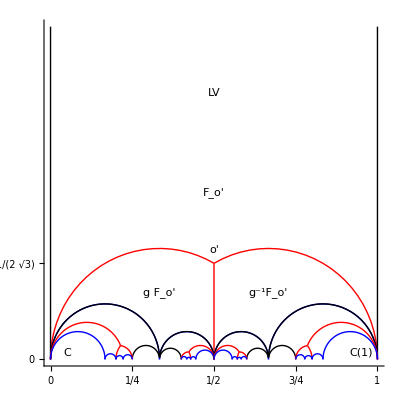

```mathematica
LiAct={Function[tau,(2tau-3)/(3tau-4)],Function[tau,tau/(3tau+1)],Function[tau,(tau-2)/(3tau-5)],Function[tau,(2tau+1)/(3tau+2)]};
GrFun=Table[{ParametricPlot[ReIm[Act[I s]],{s,0,20},PlotStyle->{Black,Thin}],
ParametricPlot[ReIm[Act[1+I s]],{s,.01,20},PlotStyle->{Black,Thin}],
ParametricPlot[ReIm[Act[1/3(1+Exp[I s])]],{s,Pi/3,Pi},PlotStyle->{Red,Thin}],
ParametricPlot[ReIm[Act[1/3(2+Exp[I s])]],{s,0,2Pi/3},PlotStyle->{Red,Thin}],
ParametricPlot[ReIm[Act[1/6(1+Exp[I s])]],{s,0,Pi},PlotStyle->{Blue,Thin}],
ParametricPlot[ReIm[Act[1/6(5+Exp[I s])]],{s,0,Pi},PlotStyle->{Blue,Thin}],
ParametricPlot[ReIm[Act[1/2+I s]],{s,0,1/2/Sqrt[3]},PlotStyle->{Red,Thin}],ParametricPlot[ReIm[Act[1/12(5+Exp[I s])]],{s,0,Pi},PlotStyle->{Blue,Thin}],
ParametricPlot[ReIm[Act[1/12(7+Exp[I s])]],{s,0,Pi},PlotStyle->{Blue,Thin}]},{Act,LiAct}];Show[{FundDomain3[0],GrFun,Graphics[{Text["LV",{1/2,.8}],Text["C(1)",{.95,0.02}],Text["C",{.05,0.02}],Text["o'",{.5,.33}],Text["F_o'",{1/2,1/2}],Text["g F_o'",{1/3,1/5}],Text["g^-1F_o'",{2/3,1/5}]}]},Axes->True,Ticks->{{0,1/6,1/5,2/9,1/4,1/3,2/5,3/7,1/2,4/7,3/5,2/3,3/4,7/9,4/5,5/6,1,4/9,5/9},{0,1/2/Sqrt[3]},1},PlotRange->{{0,1},{0,1}}]
```

## Contours of constant s=ImTD/ImT

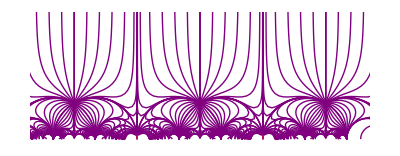

```mathematica
Gr=Module[{amax=100,afinal,slope,tauinit,tauinitlist,solution,rays,tmpplot},
tauinitlist=Join[{-10^-18,0.0001,0.002,0.025},0.1Range[9],{0.975,0.998,0.9999,1}]+I 1.;
rays=Table[
slope=Im[EichlerTD[tauinit]]/Im[EichlerT[tauinit]];
IntegralCurve[tauinit,-Conjugate[UnitDtauZch2[{1,slope,0},tau]],{0,-amax,amax}, {Im[tau]==0.01,Norm[tau-1/3]==1/3,Norm[tau-2/3]==1/3}][a],
{tauinit,tauinitlist}];
tmpplot[expr_,thickness_]:=Table[ParametricPlot[ReIm/@{ray,ray+1,ray-1},{a,0,1},PlotStyle->{{Thickness[thickness],Purple}}],{ray,expr}];
Show[FundDomainO/@Range[-1,1]/.("o'"|"o"|"C"|"LV")->"",
tmpplot[rays,Medium],
tmpplot[(rays-1)/(3rays-2),Small],tmpplot[(1-2rays)/(1-3rays),Small],
tmpplot[#,Tiny]&/@{(1+2rays)/(2+3rays),(-2+rays)/(-5+3 rays),
rays/(1+3 rays),(-1+rays)/(-5+6 rays),rays/(1+6 rays),(-1+rays)/(-8+9 rays),rays/(1+9 rays),
(1-rays)/(-4+3 rays),rays/(1-6 rays),(1-rays)/(-7+6 rays),rays/(1-9 rays),(1-rays)/(-10+9 rays)},
PlotRange->{{-.8, 1.8}, {-.02,1}}]];Show[Gr]
```

## Contours of constant (x,y)

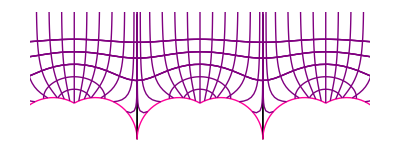

```mathematica
Module[{amax=100,afinal,tauinit,tauinitlistx,tauinitlistt,raysx,rayst,psi=0},
tauinitlistx=Join[{0.001,0.025},0.1Range[9],{0.975,0.999}]+I 1.;
tauinitlistt=1/2+I{.4,.5,.6,.7,.8};
raysx=Table[
IntegralCurve[tauinit,-I Exp[I psi]Conjugate[UnitDtauZch2[{0,1,0},tau]],{0,-amax,amax}, {Im[tau]==0.01,Norm[tau-1/3]==1/3,Norm[tau-2/3]==1/3}][a],
{tauinit,tauinitlistx}];
rayst=Table[
IntegralCurve[tauinit,-I Exp[I psi]Conjugate[UnitDtauZch2[{1,First[XY[tau,psi]],0},tau]],{0,-amax,amax}, {Im[tau]==0.01,Norm[tau-1/3]==1/3,Norm[tau-2/3]==1/3}][a],
{tauinit,tauinitlistt}];
Show[FundDomainO/@Range[-1,1]/.("o'"|"o"|"C"|"LV")->"",
Table[ParametricPlot[ReIm/@{ray,ray+1,ray-1},{a,0,1},PlotStyle->{{Thickness[Medium],Purple}}],{ray,raysx}],Table[ParametricPlot[ReIm/@{ray,ray+1,ray-1},{a,0,1},PlotStyle->{{Thickness[Medium],Purple}}],{ray,rayst}],
PlotRange->{{-.8, 1.8}, {-.02,1}}]]
```

## Image of fundamental domain in Li-Zhao coordinates

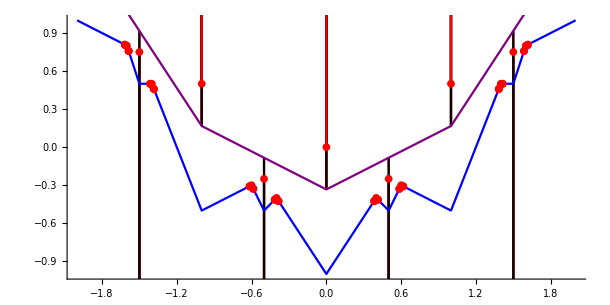

```mathematica
ClearAll[sq];
sq[tau_]:={Im[EichlerTD[tau]]/Im[EichlerT[tau]],Im[EichlerTD[tau]]/Im[EichlerT[tau]] Re[EichlerT[tau]]-Re[EichlerTD[tau]]};
Show[Table[Quiet[ParametricPlot[Evaluate[sq[tau+p]/.FundDomainRules3[0]],{a,0.001,.999},PlotStyle->{Black,Red}],{General::munfl}],{p,-2,2}],
Plot[NIntegrate[Floor[sv]+1/2,{sv,0,s}]-1/3,{s,-2,2},PlotStyle->Purple],
Plot[1/2 s^2-LPCurve[s],{s,-2,2},PlotStyle->Blue],
ListPlot[{#,1/2#^2-1/2(1-1/Denominator[#]^2)}&/@ExcepSlopes,PlotStyle->Red],
PlotRange->{{-2,2},{-1,1}}]
```

## Initial rays emerging from tau=0

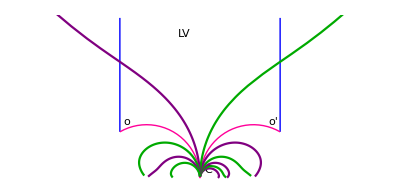

```mathematica
(*Draw rays for all O(k)[p] (Purple for even p, Green for odd p (antibranes)) *)
ClearAll[tmpPlot];
tmpPlot[psi_]:=Show[FundDomainC[0],(*FundDomain3[0],FundDomain3[-1],*)
Table[
ParametricPlot[Evaluate[ReIm/@Flatten[Table[#/(1-3p#)&[RayCh[psi+antibrane Pi][a]],{antibrane,{0,1}}]]],{a,0,1},PlotStyle->{Purple,Darker[Green]}],
{p,-2,2}],
PlotRange->{{-1.02, 1.02}, {0, 1}}];
tmpPlot[0.]
Manipulate[tmpPlot[psi],{{psi,0},-4,4,.2,Appearance->"Open"},TrackedSymbols:>{psi}];
```

## Trees for O: [1,0,1)

```mathematica
Tree101Range[0]=Tree101Range[1]=Ch[0];
Tree101Range[n_Integer?Negative]:=Fold[List,ArrayPad[{},{-n+1,0},{Ch[n-1][2],Ch[n-1/2],Ch[n]}]Join[{1},3Range[-n]]];
Tree101Range[n_Integer?Positive]:=Fold[List,ArrayPad[{},{n,0},{Ch[n][-2],Ch[n-1/2][-2],Ch[n-1]}]Join[{1},3Range[n-1]]];
```

## Trees for O_C: [0,1,1)

```mathematica
Tree011[psi_]:=Tree011Range[Ceiling[-1/2-QuantumVolume Tan[psi]]];
Tree011Range[0]:={Ch[-1][1],Ch[0]};
Tree011Range[n_Integer?Positive]:=Fold[List,ArrayPad[{},{n+1,0},{Ch[n][-1],Ch[n-1/2][-1],Ch[n-1][1]}]ArrayPad[{1,2},{0,n-1},3]];
Tree011Range[n_Integer?Negative]:=Fold[List,ArrayPad[{},{-n+1,0},{Ch[n-1][2],Ch[n-1/2],Ch[n]}]ArrayPad[{1,2},{0,-n-1},3]];
Tree011Plot[psi_,plotoptions___]:=TreeToRaysPlot[Tree011[psi],psi,plotoptions];
```